# Lab #13

## Craig Fox

Clear initial definitions

```mathematica
Remove["Global`*"]
```

Parameters

```mathematica
num=10000;
mean=13;
sigma=2;
SeedRandom[5181];
```

Generate random points following distribution

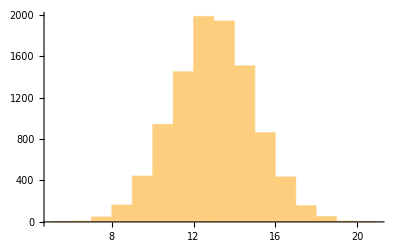

```mathematica
randomNumbers=RandomReal[2,num]-1;
distribution=(InverseErf[randomNumbers]*Sqrt[2]*sigma)+mean;
Histogram[distribution]
```

Extract bin frequencies

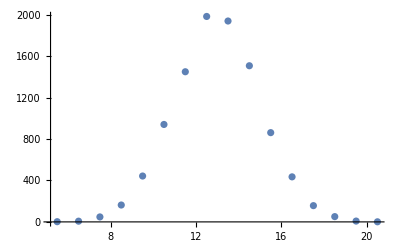

```mathematica
xlo=5;
xhi=21;
dx=1;
binCenters=Range[xlo,xhi-dx,dx]+dx/2;
binCounts=BinCounts[distribution,{xlo,xhi,dx}];
ListPlot[Transpose[{binCenters,binCounts}]]
```

Fit data to equation

```mathematica
P[x]=(1/(σ*Sqrt[2*Pi]))*Exp[-(x-u)^2/(2*σ^2)]
```

(ⅇ^(-(-u+x)^2/(2 σ^2)))/(√(2 π) σ)

Verify pdf integrates to 1

```mathematica
Integrate[P[x],{x,-Infinity,Infinity},Assumptions->σ>0]
```

1

Fitting the equation to our data

```mathematica
fit=FindFit[Transpose[{binCenters,binCounts}],n*P[x],{n,u,σ},x]
```

{n→9971.76,u→12.985,σ→1.98401}

Graphically compare equation and data points

{2005.11 ⅇ^(-0.127023 (-12.985+x)^2)}

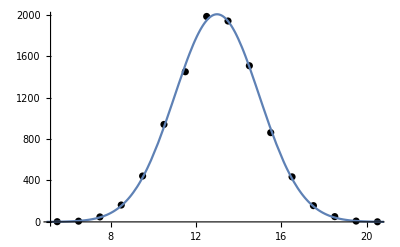

```mathematica
eq=n*P[x]/.{fit}
Show[{ListPlot[Transpose[{binCenters,binCounts}],PlotStyle->Black],Plot[eq,{x,xlo,xhi}]}]
```